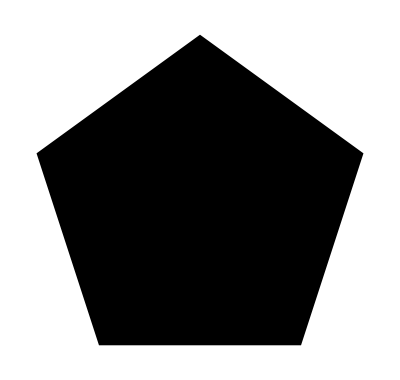

```mathematica
Graphics[Polygon[{{Sin[2π/5],Cos[2π/5]},{Sin[4π/5],-Cos[π/5]},{-Sin[4π/5],-Cos[Pi/5]},{-Sin[2π/5],Cos[2π/5]},{0,1}}]]
```

```mathematica
Clear[splineRoundedNgon]
splineRoundedNgon[n_Integer/;n≥3,roundingRadius_?(0≤#≤1&)]:=Module[{vertices,circleCenters,tangentPoints,splineControlPoints},vertices=CirclePoints[n];
circleCenters=CirclePoints[1-Sec[Pi/n] roundingRadius,n];
tangentPoints={Table[RotationMatrix[2 i Pi/n].{circleCenters[[1,1]],vertices[[1,2]]},{i,0,n-1}],Table[RotationMatrix[2 i Pi/n].{circleCenters[[-1,1]],vertices[[-1,2]]},{i,1,n}]};
splineControlPoints=Flatten[Transpose[Insert[tangentPoints,vertices,2]],1];
FilledCurve@BSplineCurve[splineControlPoints,SplineClosed->True]]
```

```mathematica
Animate[Graphics[{EdgeForm[{Thickness[0.01],Black}],FaceForm[Darker@Green],splineRoundedNgon[5,radius]}],{{radius,0,"Rounding\nradius"},0,1}]
```

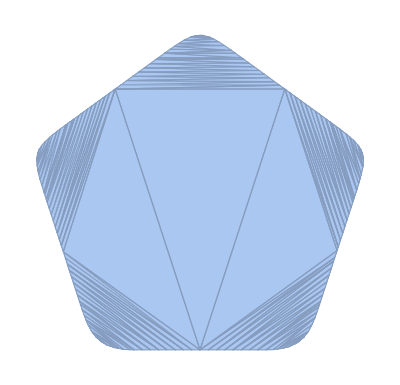

```mathematica
DiscretizeGraphics[splineRoundedNgon[5,0.3],MaxCellMeasure->0.001]
```

```mathematica
Plot3D[y Sin[5 x]+x Cos[7 y],{x,y}∈DiscretizeGraphics@splineRoundedNgon[5,0.4]]
```

-Graphics3D-

```mathematica
Clear[roundRegPoly]
roundRegPoly[n_Integer/;n≥3]:=FilledCurve@BSplineCurve[Flatten[#,1]&@Transpose[{#,#}]&@CirclePoints[n],SplineClosed->True]

Graphics[{Darker@Green,EdgeForm[{Thickness[0.01],Black}],roundRegPoly[5]},PlotRangePadding->Scaled[.1]]
```

-Graphics-

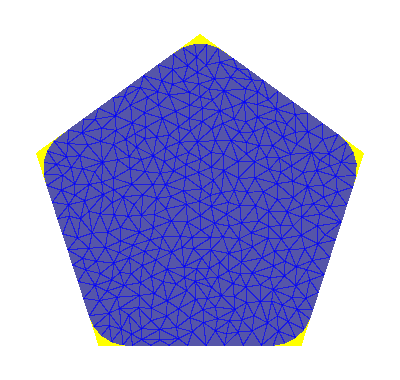

```mathematica
With[{r=1/5 (*rounding radius*)},rp=DiscretizeRegion[ImplicitRegion[RegionDistance[Polygon[CirclePoints[{1-2 Sqrt[5-2 Sqrt[5]] r,π/10},5]],{x,y}]≤r Sqrt[(5-Sqrt[5])/2],{x,y}],MaxCellMeasure->1/200]];

Graphics[{{Yellow,Polygon[CirclePoints[{1,π/10},5]]},{Opacity[2/3,Blue],MeshPrimitives[rp,2]}}]
```

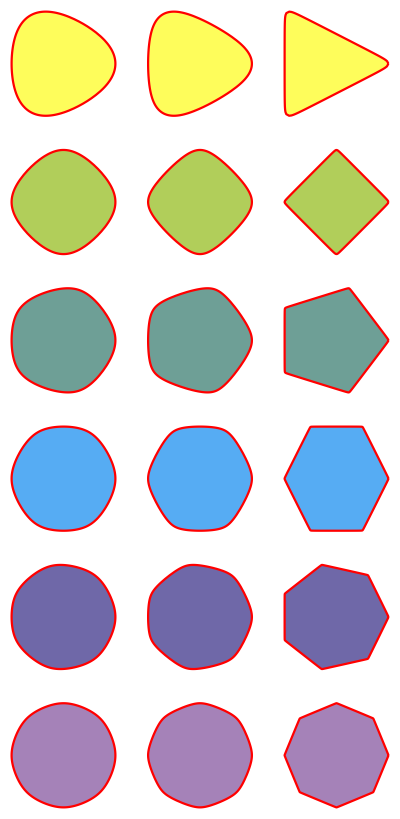

```mathematica
PolyMap[n_,z_]:=z Hypergeometric2F1[1/n,2/n,(n+1)/n,z^n]
(*Integrate[1/(1-ξ^n)^(2/n),{ξ,0,z}]*)

g=GraphicsGrid[Table[ParametricPlot[z=PolyMap[n,r (Cos[t]+I Sin[t])];{Re[z],Im[z]},{t,0,2 π},PlotRange->All,Axes->False]/.Line[l_List]:>{{Lighter[ColorData[3,"ColorList"][[n]]],Polygon[l]},{Red,Thick,Line[l]}},{n,3,8},{r,0.799,1.,0.1}],ImageSize->400]
```

```mathematica
Graphics[{EdgeForm[{JoinForm["Round"],Thickness[0.05]}],FilledCurve[Line/@Partition[CirclePoints[5],2,2,1]]},PlotRange->1.2]
```

-Graphics-

```mathematica
Graphics[{EdgeForm[{JoinForm["Round"],Thickness[0.05]}],FilledCurve[Line@CirclePoints[5]]},PlotRange->1.2]
```

-Graphics-

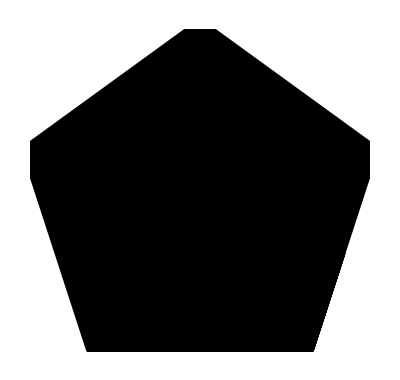

```mathematica
coords=ArrayPad[CirclePoints[5],{{0,1},{0,0}},"Periodic"];
coords=ArrayPad[coords,{{1,1},{0,0}},Mean[{coords[[1]],coords[[2]]}]];
Graphics[{Polygon[coords],JoinForm["Round"],Thickness[0.05],Line[coords]}]
```

```mathematica
arcgen[{p1_,p2_,p3_},r_,n_]:=Module[{dc=Normalize[p1-p2]+Normalize[p3-p2],cc,th},cc=p2+r dc/EuclideanDistance[dc,Projection[dc,p1-p2]];
th=Sign[Det[PadRight[{p1,p2,p3},{3,3},1]]] (π-VectorAngle[p3-p2,p1-p2])/(n-1);
NestList[RotationTransform[th,cc],p2+Projection[cc-p2,p1-p2],n-1]]

roundedPolygon[Polygon[pts_?MatrixQ],r_?NumericQ,n:(_Integer?Positive):12]:=Polygon[Flatten[arcgen[#,r,n]&/@Partition[If[TrueQ[First[pts]==Last[pts]],Most,Identity][pts],3,1,{2,-2}],1]]
```

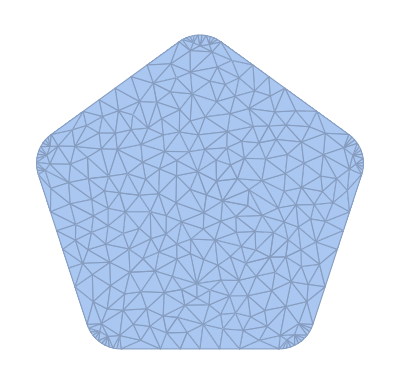

```mathematica
DiscretizeRegion[roundedPolygon[Polygon[N[CirclePoints[{1,π/10},5],20]],1/5]]
```

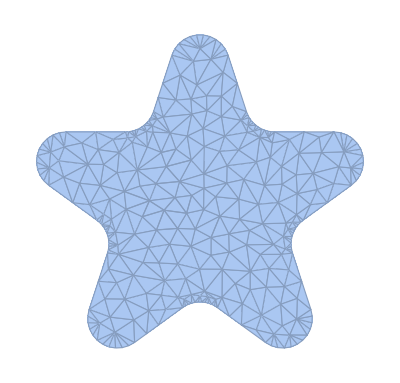

```mathematica
star=N[Riffle[CirclePoints[{1,π/10},5],RotateLeft@CirclePoints[{4 Sin[π/10]^2,-π/10},5]],20];

DiscretizeRegion[roundedPolygon[Polygon[star],1/8]]
```

```mathematica
Plot3D[Sin[6 x+Sin[6 y]],{x,y}∈roundedPolygon[Polygon[N[star,20]],1/8]]
```

-Graphics3D-

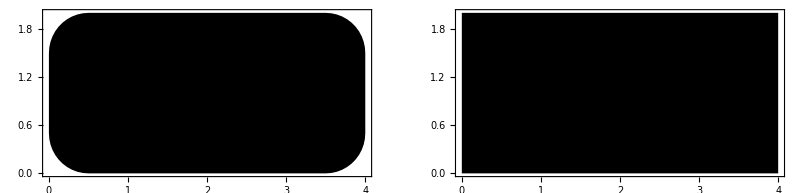

```mathematica
{Graphics[roundedPolygon[Polygon[{{0,0},{4,0},{4,2},{0,2}}//N],1/2],Frame->True],Graphics[Rectangle[{0,0},{4,2},RoundingRadius->1/2],Frame->True]}//GraphicsRow
```

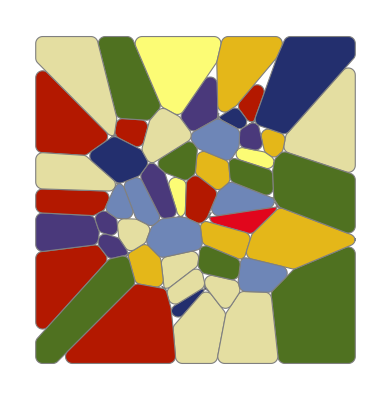

```mathematica
BlockRandom[SeedRandom[42,Method->"MersenneTwister"];
pts=RandomReal[{-2,2},{50,2}]];

BlockRandom[SeedRandom[42,Method->"ExtendedCA"];
Graphics[{Directive[ColorData[61,RandomInteger[{1,9}]],EdgeForm[Gray]],roundedPolygon[#,1/8]}&/@MeshPrimitives[VoronoiMesh[pts],2]]]
```